```mathematica
(*Odd = {0.00341978, 0.0029875, 0.00258646, 0.00214488, 0.00167539}*)
```

{0.00341978,0.0029875,0.00258646,0.00214488,0.00167539}

```mathematica
Odd = {0.00311308, 0.00292824, 0.00275608, 0.00257145, 0.00235883}
```

{0.00311308,0.00292824,0.00275608,0.00257145,0.00235883}

```mathematica
(*Even = {0.00115303, 0.00138656, 0.001624, 0.00186617, 0.00214918 }*)
```

{0.00115303,0.00138656,0.001624,0.00186617,0.00214918}

```mathematica
Even = {0.00354168,0.00368837, 0.00382674, 0.00398337, 0.00413303}
```

{0.00354168,0.00368837,0.00382674,0.00398337,0.00413303}

```mathematica
Rho = Table[Even[[i]]+Odd[[i]], {i,1,5}]
```

{0.00665476,0.00661661,0.00658282,0.00655482,0.00649186}

```mathematica
DeltaRho = Table[(Rho[[i]]-Rho[[1]])/(0.6666666^2+2*0.33333333^2), {i,1,5}]
```

{0.,-0.000057225,-0.00010791,-0.00014991,-0.00024435}

```mathematica
Mu = {0.0, 0.140, 0.200, 0.245, 0.285};
```

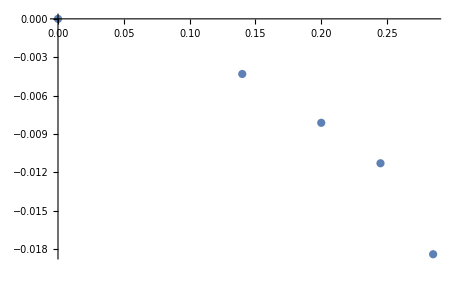

```mathematica
Plt = ListPlot[Table[{Mu[[j]], 12*2*3.14*DeltaRho[[j]]},{j,1,5}]]
```

```mathematica
Rho ={0, -0.0249035, -0.0465299, -0.0633323, -0.0889366}
```

{0,-0.0249035,-0.0465299,-0.0633323,-0.0889366}

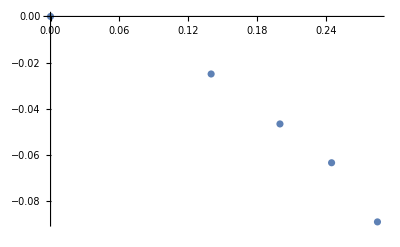

```mathematica
Plt = ListPlot[Table[{Mu[[j]], Rho[[j]]},{j,1,5}]]
```

```mathematica
0.0104422/(2*3.14)
```

0.00166277

```mathematica
0.156135/12
```

0.0130112

```mathematica
-0.00347104*12
```

-0.0416525

```mathematica
0.00347104*2*Pi
```

0.0218092

```mathematica
0.00303568/(4*Pi/(137.04)*(0.6666666^2+2*0.33333333^2))
```

0.0496575

```mathematica
0.004553520637492858*2*3.14
```

0.0285961

```mathematica
0.285*3*3.14
```

2.6847

```mathematica
Mu = {0.0, 0.140, 0.200, 0.245, 0.285};
```

```mathematica
MuPlot = Table[Mu[[i]]*12, {i,1,5}]
```

{0.,1.68,2.4,2.94,3.42}

```mathematica
Sigma = {0, -0.0190941, -0.0328886, -0.0497356, -0.04244}
```

{0,-0.0190941,-0.0328886,-0.0497356,-0.04244}

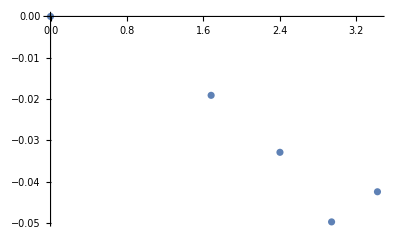

```mathematica
Plt = ListPlot[Table[{MuPlot[[j]], Sigma[[j]]},{j,1,5}]]
```

```mathematica
Sigma2 = {0, -0.0151565, -0.0427912, -0.0281821, -0.0383564}
```

{0,-0.0151565,-0.0427912,-0.0281821,-0.0383564}

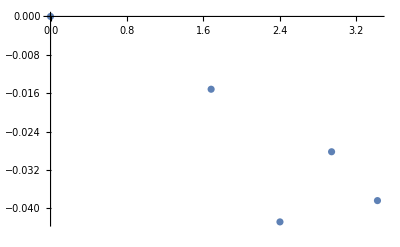

```mathematica
Plt2 = ListPlot[Table[{MuPlot[[j]], Sigma2[[j]]},{j,1,5}]]
```

```mathematica
SigmaBGNew = {0,-0.0169445, -0.0481672, -0.0349216, -0.0433315};
```

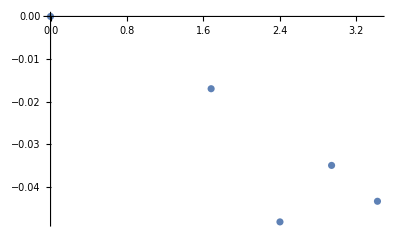

```mathematica
Plt3 = ListPlot[Table[{MuPlot[[j]], SigmaBGNew[[j]]},{j,1,5}]]
```

```mathematica
SigmaBGNew03 = {0,-0.00387056,-0.0265106,0.0216885,-0.00085241}
```

{0,-0.00387056,-0.0265106,0.0216885,-0.00085241}

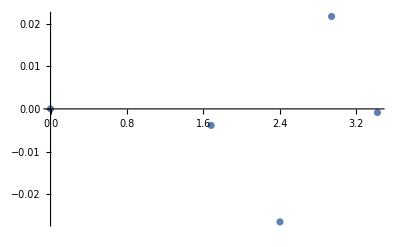

```mathematica
Plt4 = ListPlot[Table[{MuPlot[[j]], SigmaBGNew03[[j]]},{j,1,5}]]
```